```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Importing data

```mathematica
(*observed error, flag == 0,
 error grid, flag == 1 and 
error velocity flag == 2
num sol flag == 3
adjoint sol == 4*)
importdata[cycle_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/error_observed_cycle",ToString[cycle],".txt"],
flag == 1,
filename=StringJoin["../",outputdir,"/error_grid_cycle",ToString[cycle],".txt"],

flag == 2,
filename=StringJoin["../",outputdir,"/error_velocity_cycle",ToString[cycle],".txt"],
flag == 3,
filename=StringJoin["../",outputdir,"/result_cycle",ToString[cycle],".txt"],
flag == 4,
filename=StringJoin["../",outputdir,"/result_cycle",ToString[cycle],".txt"],
flag == 5,
filename=StringJoin["../",outputdir,"/fe_index_cycle",ToString[cycle],".txt"]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]
]

SortData[data_]:=Module[{indices},
indices = Ordering[data⟦All,1⟧,All,GreaterEqual];
data⟦indices,All⟧
]
```

## Results

```mathematica
M6sol = GetSolutionPoisson[6,0.1,1,bcMBC[6]]⟦3⟧;
M50sol = GetSolutionPoisson[50,0.1,1,bcMBC[50]]⟦3⟧;
```

```mathematica
Clear[errorObs,errorGrid,errorVelocity,resultPrimal,resultAdj,feIndex];
```

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"2x1v_moments_wall_Adp"];
errorGrid[cycle]=importdata[cycle,1,"2x1v_moments_wall_Adp"];
errorVelocity[cycle]=importdata[cycle,2,"2x1v_moments_wall_Adp"];
resultPrimal[cycle]=importdata[cycle,3,"2x1v_moments_wall_Adp"];
resultAdj[cycle]=importdata[cycle,4,"2x1v_moments_wall_Adp"];
feIndex[cycle]=importdata[cycle,5,"2x1v_moments_wall_Adp"],{cycle,0,4}];
```

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle4.txt

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

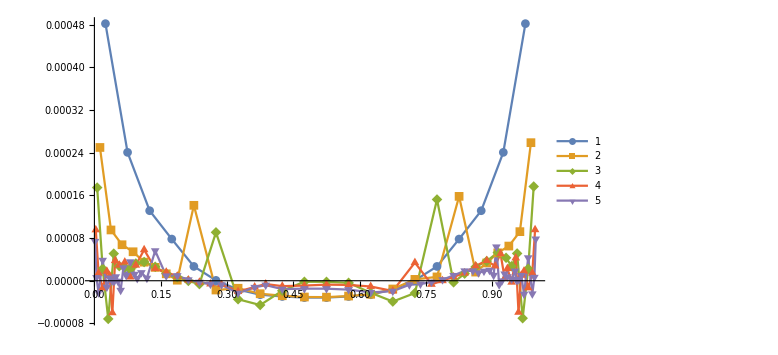

```mathematica
ListPlot[{SortData[errorGrid[0]]⟦All,{1,3}⟧,SortData[errorGrid[1]]⟦All,{1,3}⟧,SortData[errorGrid[2]]⟦All,{1,3}⟧,SortData[errorGrid[3]]⟦All,{1,3}⟧,SortData[errorGrid[4]]⟦All,{1,3}⟧},ImageSize->Large,Joined->True,PlotRange->Full,PlotLegends->Automatic,PlotMarkers->Automatic]
```

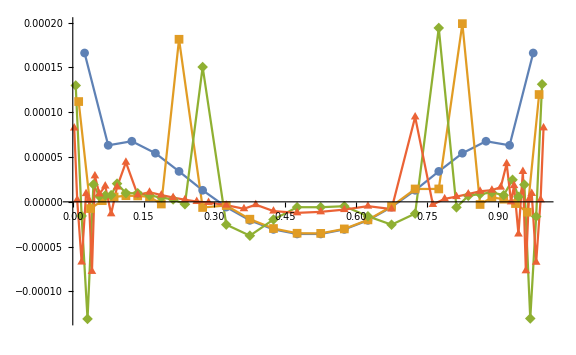

```mathematica
ListPlot[{SortData[errorVelocity[0]]⟦All,{1,3}⟧,SortData[errorVelocity[1]]⟦All,{1,3}⟧,SortData[errorVelocity[2]]⟦All,{1,3}⟧,SortData[errorVelocity[3]]⟦All,{1,3}⟧(*,SortData[errorVelocity[4]]⟦All,{1,3}⟧*)},ImageSize->Large,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

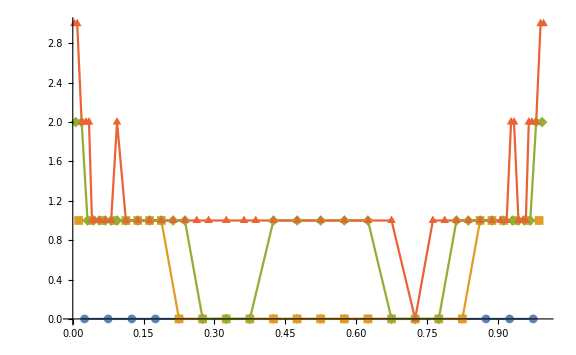

```mathematica
ListPlot[{SortData[feIndex[0]]⟦All,{1,3}⟧,SortData[feIndex[1]]⟦All,{1,3}⟧,SortData[feIndex[2]]⟦All,{1,3}⟧,SortData[feIndex[3]]⟦All,{1,3}⟧(*,SortData[errorVelocity[4]]⟦All,{1,3}⟧*)},ImageSize->Large,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

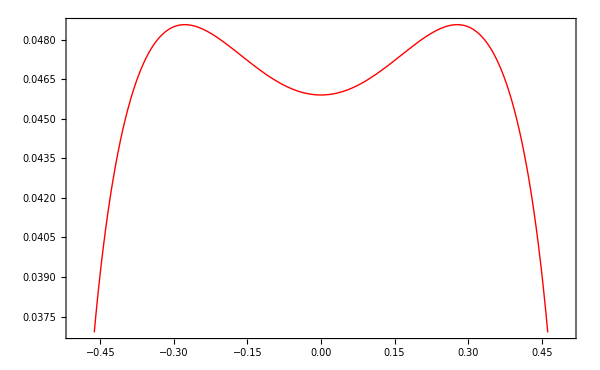

```mathematica
Plot[M50sol,{x,-0.5,0.5}]
```

```mathematica
NIntegrate[M50sol-M6sol,{x,-0.5,0.5}]/0.001153
```

1.26059

```mathematica
convgAdp = Import["../2x1v_moments_wall_Adp/convergence_table_adaptive.txt","Table"];
convgUni = Import["../2x1v_moments_wall_Adp/convergence_table_uniform.txt","Table"];
```

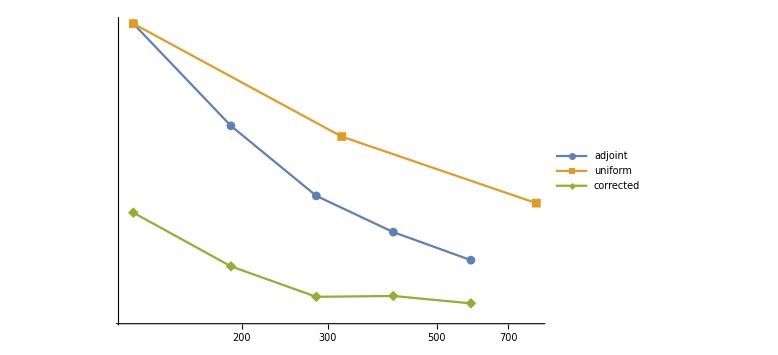

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgAdp⟦2;;-1,{6,13}⟧(*,convgAdp⟦2;;-1,{6,9}⟧,convgAdp⟦2;;-1,{6,11}⟧*)},Joined->True,PlotLegends->{"adjoint","uniform","corrected"},PlotMarkers->Automatic,ImageSize->Large,PlotRange->Full]
```

```mathematica
CForm[Chop[Simplify[GetSolutionPoisson[14,0.1,1,bcMBC[14]]⟦3⟧]]]/.{Power->pow,Cosh->cosh}
```

0.05653013082799942 - 0.00003792694823015286*cosh(1.64277980395364*x) - 0.0014402108667994624*cosh(2.0483113377580193*x) - 
   0.00530163981896668*cosh(2.6857066212139475*x) - 0.003996181490901356*cosh(4.230009784703013*x) - 
   0.00006758700357029971*cosh(12.325411809002668*x) + 0.13333333333333333*pow(x,2) - 0.2777777777777778*pow(x,4)